Strain Demo - Modified

Notes:
1. These data sets are common in that they represent the same square reference configuration, and the strain calculations take place at each corner with the circumferentially-nearest neighbors.

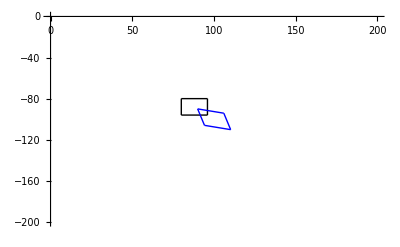

-Graphics-

((0.) | (0.26125)
(0.26125) | (0.))

((0.) | (0.26125)
(0.26125) | (0.))

((0.) | (0.26125)
(0.26125) | (0.))

-Graphics-

-Graphics-

-Graphics-

«8 more identical outputs»

```mathematica
(*Initialize*)
ClearAll["Global`*"]
ROIwidth=ROIheight=200;  (* Use 200 *)


(*User input*)
dataSet=8;
offsetX=offsetY=80;  (* Use 80 *)
pointSpreadFactor=2;  (*Use 2 for sets 1 through 8, 4 for set 9 *)

(*Scales the distance between points, horizontally and vertically*)
migrationDistThresh=5;


(*Determine point sets*)
pt={{0,0},
{8,0},
{8,8},
{0,8}};
ptStar=N[Switch[dataSet,
1,
{{16,24},
{24,24},
{24,32},
{16,32}},
2,
{{-1.047,1.047},
{6.953,-1.047},
{9.047,6.953},
{1.047,9.047}},
3,
{{10,10},
{34,10},
{34,18},
{10,18}},
4,
{{13,10},
{21,10},
{21,34},
{13,34}},
5,
{{10,10},
{22,10},
{22,14},
{10,14}},
6,
{{10,10},
{18,12.09},
{18,20.09},
{10,18}},
7,
{{10,10},
{18,10},
{15.91,18},
{7.91,18}},
8,
{{10,10},
{18,12.09},
{20.09,20.09},
{12.09,18}},
9,
{{10,15},
{22,15.8},
{22,25.8},
{10,25}}
]];


(*Apply tranformation to properly range point sets*)
(*  Spread points*)
applyPtSpreadFactor[array_]:=Module[{minX=Min[ Table[ array[[p,1]],{p,1,4} ] ],
minY=Min[ Table[ array[[p,2]],{p,1,4} ] ],
arrayMod=0},

arrayMod=array-Table[{minX,minY},{i,1,4}];
arrayMod=Table[ pointSpreadFactor*arrayMod[[p]],{p,1,4} ];
arrayMod=arrayMod+Table[{minX,minY},{i,1,4}];
arrayMod
];

pt=applyPtSpreadFactor[pt];
ptStar=applyPtSpreadFactor[ptStar];

(*  Offset*)
offset={{offsetX,offsetY},{offsetX,offsetY},{offsetX,offsetY},{offsetX,offsetY}};
pt=pt+offset;
ptStar=ptStar+offset;


(*Compute strain at each point, using the circumferentially-nearest neighbors*)
Clear[a,b,c,d,e,f]
ux[x_,y_]=a*x+b*y+c;
uy[x_,y_]=d*x+e*y+f;
rule1=Solve[
Flatten[Table[{ux[pt[[p,1]],pt[[p,2]]]==ptStar[[p,1]]-pt[[p,1]],uy[pt[[p,1]],pt[[p,2]]]==ptStar[[p,2]]-pt[[p,2]]},
{p,{1,2,3}}]],
{a,b,c,d,e,f}];
eps1={{D[ux[x,y]/.rule1,x],.5*(D[ux[x,y]/.rule1,y]+D[uy[x,y]/.rule1,x])},
{.5*(D[ux[x,y]/.rule1,y]+D[uy[x,y]/.rule1,x]),D[uy[x,y]/.rule1,y]}};

rule2=Solve[
Flatten[Table[{ux[pt[[p,1]],pt[[p,2]]]==ptStar[[p,1]]-pt[[p,1]],uy[pt[[p,1]],pt[[p,2]]]==ptStar[[p,2]]-pt[[p,2]]},
{p,{2,3,4}}]],
{a,b,c,d,e,f}];
eps2={{D[ux[x,y]/.rule2,x],.5*(D[ux[x,y]/.rule2,y]+D[uy[x,y]/.rule2,x])},
{.5*(D[ux[x,y]/.rule2,y]+D[uy[x,y]/.rule2,x]),D[uy[x,y]/.rule2,y]}};

rule3=Solve[
Flatten[Table[{ux[pt[[p,1]],pt[[p,2]]]==ptStar[[p,1]]-pt[[p,1]],uy[pt[[p,1]],pt[[p,2]]]==ptStar[[p,2]]-pt[[p,2]]},
{p,{3,4,1}}]],
{a,b,c,d,e,f}];
eps3={{D[ux[x,y]/.rule3,x],.5*(D[ux[x,y]/.rule3,y]+D[uy[x,y]/.rule3,x])},
{.5*(D[ux[x,y]/.rule3,y]+D[uy[x,y]/.rule3,x]),D[uy[x,y]/.rule3,y]}};


(*Reverse all points across the horizontal axis, for display in images*)
pt=Table[{pt[[p,1]],-pt[[p,2]]},{p,1,Length[pt]}];
ptStar=Table[{ptStar[[p,1]],-ptStar[[p,2]]},{p,1,Length[ptStar]}];


(*Calculate parameters and functions for linear image sequence*)
pMax=4;  (*Number of points*)
a=Table[0,{p,1,pMax}];
b=Table[0,{p,1,pMax}];
c=Table[0,{p,1,pMax}];
d=Table[0,{p,1,pMax}];
zStep=1;  (*z ranges from 0 to 1, so zStep == 1 is an upper bound*)
For[p=1,p≤pMax,p++,
{b[[p]]=pt[[p,1]];
d[[p]]=pt[[p,2]];
a[[p]]=ptStar[[p,1]]-b[[p]];
c[[p]]=ptStar[[p,2]]-d[[p]];
}]

zStep=Min[migrationDistThresh/a,migrationDistThresh/c];

x[z_,p_]:=a[[p]]*z+b[[p]];
y[z_,p_]:=c[[p]]*z+d[[p]];


(*Generate single plots*)
plotRange={{0,ROIwidth},{-ROIheight,0}};
plt1=ListLinePlot[Table[{pt[[p]],pt[[1+Mod[p,4]]]},{p,1,4}],
PlotStyle->Black,
PlotRange->plotRange];
plt2=ListLinePlot[Table[{ptStar[[p]],ptStar[[1+Mod[p,4]]]},{p,1,4}],
PlotStyle->Blue];
plt3=ListPlot[Table[pt[[p]],{p,1,4}],
PlotStyle->{Green,PointSize[Medium]},
PlotRange->plotRange,
Axes->False,
AspectRatio->1];
plt4=ListPlot[Table[ptStar[[p]],{p,1,4}],
PlotStyle->{Green,PointSize[Medium]},
PlotRange->plotRange,
Axes->False,
AspectRatio->1];


(*Display all output*)
Show[plt1,plt2]
Show[plt3,plt4]
eps1//MatrixForm
eps2//MatrixForm
eps3//MatrixForm


(*Loop and generate an image sequence, such that the maximum dynamic migration distance of any point (vertically or horizontally, not absolutely) is migrationDistThresh *)
count=1;
For[z=0,z≤1,z+=0.1,{
plt=ListPlot[Table[{x[z,p],y[z,p]},{p,1,pMax}],
PlotStyle->{Green,PointSize[Medium]},
PlotRange->plotRange,
Axes->False,
AspectRatio->1];

rasterPlot=Rasterize[plt,ImageSize->{ROIwidth,ROIheight}];

Export["/home/administrator/Documents/test-correlate/Test_Data_Programmatic/test"<>ToString[dataSet-1]<>"plt"<>ToString[count-1]<>".bmp",rasterPlot,
"BMP"];

Print[rasterPlot];
count++;
}]
```

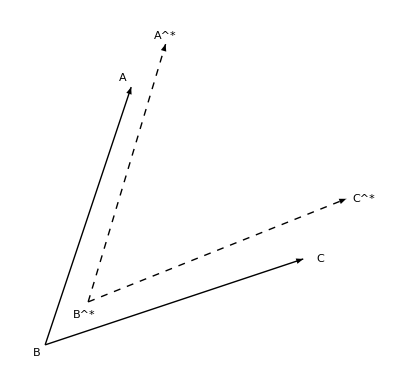

```mathematica
ClearAll["Global`*"]

pt={{1,3},{0,0},{3,1}};
ptStar={{1.1,3.2},{0.2,0.2},{3.2,1.4}};
ptStar+=0.3;

text1=Graphics[{
Text[Style["A",Medium],pt[[1]]+{-.1,.1}],
Text[Style["B",Medium],pt[[2]]+{-.1,-.1}],
Text[Style["C",Medium],pt[[3]]+{.2,0}]
}];
text1Star=Graphics[{
Text[Style[Superscript["A",Style["*",Medium]],Medium],ptStar[[1]]+{0,.1}],
Text[Style[Superscript["B",Style["*",Medium]],Medium],ptStar[[2]]+{-.05,-.15}],
Text[Style[Superscript["C",Style["*",Medium]],Medium],ptStar[[3]]+{.2,0}]
}];

arrow1=Graphics[
Arrow[
Table[pt[[i]],{i,2,1,-1}]
]
];
arrow2=Graphics[Arrow[
Table[pt[[i]],{i,2,3,1}]]];

arrow1Star=Graphics[{Thick,Dashed,Arrow[
Table[ptStar[[i]],{i,2,1,-1}]]}];
arrow2Star=Graphics[{Thick,Dashed,Arrow[
Table[ptStar[[i]],{i,2,3,1}]]}];

Show[arrow1,arrow2,arrow1Star,arrow2Star,text1,text1Star]
```

```mathematica
pt=Table[{pt[[i,1]],-pt[[i,2]]},{i,1,4}]
ptStar=Table[{ptStar[[i,1]],-ptStar[[i,2]]},{i,1,4}]
```

{{0,0},{32,0},{32,32},{0,32}}

{{10.,15.},{58.,18.2},{58.,58.2},{10.,55.}}